```mathematica
lr;
Clear[x];
stateXPrime=bool[({{xp[1,1], xp[1,2], xp[1,3], xp[1,4], xp[1,5]}, {xp[2,1], xp[2,2], xp[2,3], xp[2,4], xp[2,5]}, {xp[3,1], xp[3,2], xp[3,3], xp[3,4], xp[3,5]}, {xp[4,1], xp[4,2], xp[4,3], xp[4,4], xp[4,5]}, {xp[5,1], xp[5,2], xp[5,3], xp[5,4], xp[5,5]}})=loob[({{0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 1, 1, 1, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}})]];
plt[stateX];
```

```mathematica
form=and@Flatten@Array[

formula

,{5,5}];
```

```mathematica
varlist=Flatten@Array[x,{5,5}];
```

```mathematica
lr
```

```mathematica
bool[Array[x,{5,5}]/.Thread[varlist->SatisfiabilityInstances[form,varlist][[1]]]
]//Grid
```

1 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0

```mathematica
life44
```

```mathematica
X1=({{1, 1, 0, 1, 1}, {0, 0, 0, 0, 0}, {1, 1, 1, 1, 1}, {0, 0, 1, 0, 0}, {0, 0, 1, 0, 0}})//FullForm
```

Grid[List[List[1,1,0,1,1],List[0,0,0,0,0],List[1,1,1,1,1],List[0,0,1,0,0],List[0,0,1,0,0]],Rule[ItemSize,List[Automatic,Automatic]]]

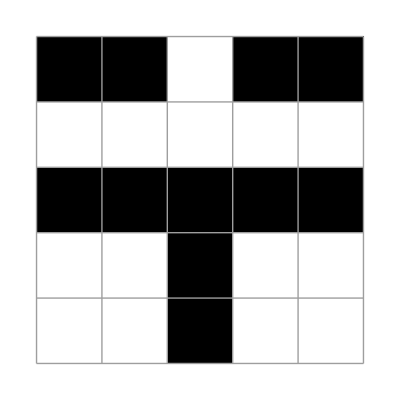
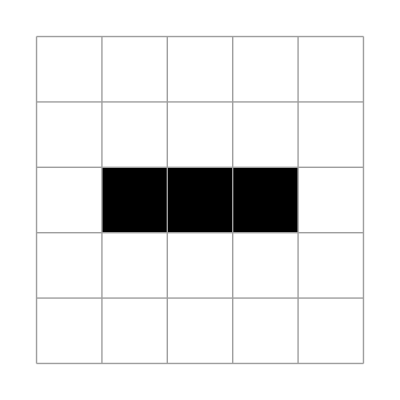
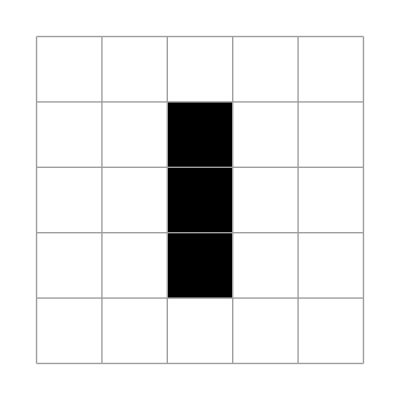
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
lr;X1=bool[oneStepBack];
MessageDialog[X1];
plt/@NestList[updateLife2[{5,5}][ #]&,
X1,3]
```